```mathematica
D[2Sqrt[x-2k],x]^3+2 D[2Sqrt[x-2k],x,x]
```

0

```mathematica
Integrate[1/x^3,x]
```

-1/(2 x^2)

```mathematica
Integrate[1/Sqrt[x-2k],x]
```

2 √(-2 k+x)

```mathematica
Solve[x^2+x-Sin[f]==0,x]
```

{{x→1/2 (-1-√(1+4 Sin[f]))},{x→1/2 (-1+√(1+4 Sin[f]))}}

```mathematica
Integrate[Sqrt[1+4 Sin[x]],x]
```

-2 √5 EllipticE[1/4 (π-2 x),8/5]

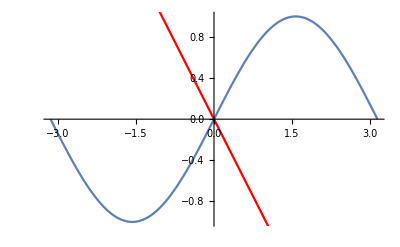

```mathematica
Show[
Plot[Sin[x],{x,-π,π}],
Plot[-x,{x,-π,π},PlotStyle->Red]
]
```

```mathematica
FindRoot[Sin[x]==-x,{x,1}]
```

{x→0.}

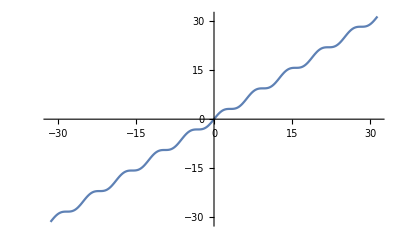

```mathematica
Plot[Sin[x]+x,{x,-10π,10π}]
```

```mathematica
Integrate[Csc[x],x]
```

-Log[Cos[x/2]]+Log[Sin[x/2]]

```mathematica
Integrate[ArcTan[Exp[-x]],x]
```

x ArcTan[ⅇ^-x]+1/2 ⅈ (x (Log[1-ⅈ ⅇ^x]-Log[1+ⅈ ⅇ^x])-PolyLog[2,-ⅈ ⅇ^x]+PolyLog[2,ⅈ ⅇ^x])

```mathematica
Integrate[Integrate[ArcTan[Exp[-x]],x],x]
```

1/4 (x^2 (2 ArcTan[ⅇ^-x]+ⅈ (Log[1-ⅈ ⅇ^x]-Log[1+ⅈ ⅇ^x]))-2 ⅈ PolyLog[3,-ⅈ ⅇ^x]+2 ⅈ PolyLog[3,ⅈ ⅇ^x])

```mathematica
FullSimplify[Integrate[Integrate[Integrate[ArcTan[Exp[-x]],x],x],x]]
```

1/6 (x^3 (ArcCot[ⅇ^x]+ArcTan[ⅇ^x])-3 ⅈ PolyLog[4,-ⅈ ⅇ^x]+3 ⅈ PolyLog[4,ⅈ ⅇ^x])

```mathematica
N[Table[π x^3/12+I/2(PolyLog[4,I Exp[x]]-PolyLog[4,-I Exp[x]]),{x,1,100,10}]]
```

{-2.30517+0. ⅈ,-21.3168+0. ⅈ,-40.6957+0. ⅈ,-60.0747+0. ⅈ,-79.4536+0. ⅈ,-98.8325+0. ⅈ,-118.211+0. ⅈ,-137.59+0. ⅈ,-156.969+0. ⅈ,-176.348+0. ⅈ}

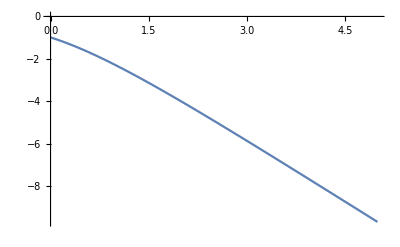

```mathematica
Plot[Re[π x^3/12+I/2(PolyLog[4,I Exp[x]]-PolyLog[4,-I Exp[x]])],{x,0,5},AxesOrigin->{0,0}]
```

```mathematica
Integrate[1/Sqrt[Cos[x]],x]
```

2 EllipticF[x/2,2]

```mathematica
Integrate[2 JacobiSN[I x/2,2],x]
```

-2 ⅈ √2 Log[-√2 JacobiCN[(ⅈ x)/2,2]+JacobiDN[(ⅈ x)/2,2]]

```mathematica
DSolve[D[Rm[r],r,r]+1/r D[Rm[r],r]-m^2/r^2 Rm[r]==0,Rm[r],r]
```

{{Rm[r]→C[1] Cosh[m Log[r]]+ⅈ C[2] Sinh[m Log[r]]}}

```mathematica
DSolve[D[Rm[r],r,r]+1/r D[Rm[r],r]==0,Rm[r],r]
```

{{Rm[r]→C[2]+C[1] Log[r]}}

```mathematica
DSolve[{D[Rm[r],r,r]+1/r D[Rm[r],r]-m^2/r^2 Rm[r]==0,Rm[R]==0},Rm[r],r]
```

{{Rm[r]→C[1] Cosh[m Log[r]]-C[1] Coth[m Log[R]] Sinh[m Log[r]]}}

```mathematica
DSolve[{D[Rm[r],r,r]+1/r D[Rm[r],r]-m^2/r^2 Rm[r]==0,Rm[0]==0,Rm[R]==0},Rm[r],r]
```

DSolve::bvlim: For some branches of the general solution, unable to compute the limit at the given points. Some of the solutions may be lost.

{}

```mathematica
DSolve[D[ϕ[r,θ],{r,2}]+1/r D[ϕ[r,θ],r]+1/r^2 D[ϕ[r,θ],{θ,2}]==-q/r DiracDelta[r]DiracDelta[θ],ϕ[r,θ],{r,θ}]
```

DSolve[(ϕ^(0,2)[r,θ])/r^2+(ϕ^(1,0)[r,θ])/r+ϕ^(2,0)[r,θ]==-(q DiracDelta[r] DiracDelta[θ])/r,ϕ[r,θ],{r,θ}]

```mathematica
Block[
{f,r,θ,n,A0,B0},
f[r_,θ_]:=A0+B0 Log[r]+B0/2 Log[Cos[θ]^(4/n)+Sin[θ]^(4/n)];
FullSimplify[
(Cos[θ]^(4(1-1/n))+Sin[θ]^(4(1-1/n)))D[f[r,θ],{r,2}]+n Sin[2θ]/2/r D[f[r,θ],r,θ](Sin[θ]^(2(1-1/n))-Cos[θ]^(2(1-1/n)))+n^2/2/r^2 D[f[r,θ],{θ,2}](Sin[θ]^3+Cos[θ]^3)/Sin[2θ]+(n-1)/r/Cos[θ]D[f[r,θ],r](Sin[θ]^2+2/n Cos[θ]^3 Sin[θ]^(2-4/n))+n/4/r^2 D[f[r,θ],θ](Sin[θ](n-(n-2)Tan[θ]^2+2 Cos[θ]^(3-4/n))+Cos[θ]((n-2)Cot[θ]^2-n-2 Sin[θ]^(3-4/n)))
]
]
```

1/(8 r^2)B0 (8 (-1+n) Sec[θ] (Sin[θ]^2+(2 Cos[θ]^3 Sin[θ]^(2-4/n))/n)-8 (Cos[θ]^(4-4/n)+Sin[θ]^(4-4/n))-(4 (1+Cot[θ]^3) Sec[θ]^3 (n Cos[θ]^(8/n) Sin[θ]^2+(-4+n) Cos[θ]^(4/n) Sin[θ]^(4/n)+n Cos[θ]^2 Sin[θ]^(8/n)))/(Cos[θ]^(4/n)+Sin[θ]^(4/n))^2+1/(Cos[θ]^(4/n)+Sin[θ]^(4/n))4 Cos[θ] Sin[θ] (-Cos[θ]^(-2+4/n)+Sin[θ]^(-2+4/n)) (Cos[θ] (-n+(-2+n) Cot[θ]^2-2 Sin[θ]^(3-4/n))+Sin[θ] (n+2 Cos[θ]^(3-4/n)-(-2+n) Tan[θ]^2)))

```mathematica
Manipulate[
Sum[(8 (-1+n) Sec[θ] (Sin[θ]^2+(2 Cos[θ]^3 Sin[θ]^(2-4/n))/n)-8 (Cos[θ]^(4-4/n)+Sin[θ]^(4-4/n))-(4 (1+Cot[θ]^3) Sec[θ]^3 (n Cos[θ]^(8/n) Sin[θ]^2+(-4+n) Cos[θ]^(4/n) Sin[θ]^(4/n)+n Cos[θ]^2 Sin[θ]^(8/n)))/(Cos[θ]^(4/n)+Sin[θ]^(4/n))^2+1/(Cos[θ]^(4/n)+Sin[θ]^(4/n))4 Cos[θ] Sin[θ] (-Cos[θ]^(-2+4/n)+Sin[θ]^(-2+4/n)) (Cos[θ] (-n+(-2+n) Cot[θ]^2-2 Sin[θ]^(3-4/n))+Sin[θ] (n+2 Cos[θ]^(3-4/n)-(-2+n) Tan[θ]^2))),{θ,0.01,π/2-0.01,0.01}]
,{n,2.01,10}
]
```

```mathematica
D[Cos[x]^(2/n),x]
```

-(2 Cos[x]^(-1+2/n) Sin[x])/n

```mathematica
D[Sin[x]^(2/n),x]
```

(2 Cos[x] Sin[x]^(-1+2/n))/n

```mathematica
FullSimplify[Det[
{
{
Cos[θ]^(4/n)+Sin[θ]^(4/n),2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1))
},
{
2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1)),4r^2/n^2(Sin[θ]^2 Cos[θ]^(4/n-2)+Cos[θ]^2 Sin[θ]^(4/n-2))
}
}
]]
```

(4 r^2 Cos[θ]^(-2+4/n) Sin[θ]^(-2+4/n))/n^2

```mathematica
FullSimplify[Inverse[
{
{
Cos[θ]^(4/n)+Sin[θ]^(4/n),2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1))
},
{
2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1)),4r^2/n^2(Sin[θ]^2 Cos[θ]^(4/n-2)+Cos[θ]^2 Sin[θ]^(4/n-2))
}
}
]]
```

{{Cos[θ]^(4-4/n)+Sin[θ]^(4-4/n),(n Cos[θ] Sin[θ] (-Cos[θ]^(2-4/n)+Sin[θ]^(2-4/n)))/(2 r)},{(n Cos[θ] Sin[θ] (-Cos[θ]^(2-4/n)+Sin[θ]^(2-4/n)))/(2 r),(n^2 Cos[θ]^2 Sin[θ]^2 (Cos[θ]^(-4/n)+Sin[θ]^(-4/n)))/(4 r^2)}}

```mathematica
FullSimplify[{
{
Cos[θ]^(4/n)+Sin[θ]^(4/n),2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1))
},
{
2r/n (Cos[θ]Sin[θ]^(4/n-1)-Sin[θ]Cos[θ]^(4/n-1)),4r^2/n^2(Sin[θ]^2 Cos[θ]^(4/n-2)+Cos[θ]^2 Sin[θ]^(4/n-2))
}
}.{{Cos[θ]^(4-4/n)+Sin[θ]^(4-4/n),(n Cos[θ] Sin[θ] (-Cos[θ]^(2-4/n)+Sin[θ]^(2-4/n)))/(2 r)},{(n Cos[θ] Sin[θ] (-Cos[θ]^(2-4/n)+Sin[θ]^(2-4/n)))/(2 r),(n^2 Cos[θ]^2 Sin[θ]^2 (Cos[θ]^(-4/n)+Sin[θ]^(-4/n)))/(4 r^2)}}]
```

{{1,0},{0,1}}

```mathematica
Block[
{f,r,θ,n,A0,B0},
f[r_,θ_]:=A0+B0 Log[r]+B0/2 Log[Cos[θ]^(4/n)+Sin[θ]^(4/n)];
FullSimplify[
n/(2 r (Sin[θ]Cos[θ])^(2/n-1))(
D[2r/n(Sin[θ]Cos[θ])^(2/n-1)(Sin[θ]^(4-4/n)+Cos[θ]^(4-4/n))D[f[r,θ],r],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],θ],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],r],θ]
+D[n/2/r (Sin[θ]Cos[θ])^(2/n+1)(Sin[θ]^(-4/n)+Cos[θ]^(-4/n))D[f[r,θ],θ],θ]
)
]
]
```

0

```mathematica
Block[
{f,r,θ,n,m,Am,Bm,Cm,Dm},
f[r_,θ_]:=r^m (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(m/2)Sin[m ArcTan[(Tan[θ])^(2/n)]];
FullSimplify[
n/(2r(Sin[θ]Cos[θ])^(2/n-1))(
D[2r/n(Sin[θ]Cos[θ])^(2/n-1)(Sin[θ]^(4-4/n)+Cos[θ]^(4-4/n))D[f[r,θ],r],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],θ],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],r],θ]
+D[n/2/r (Sin[θ]Cos[θ])^(2/n+1)(Sin[θ]^(-4/n)+Cos[θ]^(-4/n))D[f[r,θ],θ],θ]
)
,Assumptions->n>0]
]
```

-1/((1+Tan[θ]^(4/n))^2)m r^(-2+m) Cos[θ]^(-4/n) Sin[θ]^(-4/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(-1+m/2) (-Sin[θ]^(4/n)+Cos[θ]^(4/n) Tan[θ]^(4/n)) (2 Cos[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)+Sin[θ]^(4/n)) Tan[θ]^(2/n)+m Sin[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)-Sin[θ]^(4/n) Tan[θ]^(4/n)))

```mathematica
Manipulate[Plot[-1/((1+Tan[θ]^(4/n))^2)m r^(-2+m) Cos[θ]^(-4/n) Sin[θ]^(-4/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(-1+m/2) (-Sin[θ]^(4/n)+Cos[θ]^(4/n) Tan[θ]^(4/n)) (2 Cos[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)+Sin[θ]^(4/n)) Tan[θ]^(2/n)+m Sin[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)-Sin[θ]^(4/n) Tan[θ]^(4/n))),{θ,0,π/2}],{m,1,10},{n,2.01,10}]
```

```mathematica
Block[
{f,r,θ,n,m,Am,Bm,Cm,Dm},
f[r_,θ_]:=r^(-m) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(-m/2)Sin[m ArcTan[(Tan[θ])^(2/n)]];
FullSimplify[
n/(2r(Sin[θ]Cos[θ])^(2/n-1))(
D[2r/n(Sin[θ]Cos[θ])^(2/n-1)(Sin[θ]^(4-4/n)+Cos[θ]^(4-4/n))D[f[r,θ],r],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],θ],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],r],θ]
+D[n/2/r (Sin[θ]Cos[θ])^(2/n+1)(Sin[θ]^(-4/n)+Cos[θ]^(-4/n))D[f[r,θ],θ],θ]
)
]
]
```

-1/((1+Tan[θ]^(4/n))^2)m r^(-2-m) Cos[θ]^(-4/n) Sin[θ]^(-4/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(-1-m/2) (-Sin[θ]^(4/n)+Cos[θ]^(4/n) Tan[θ]^(4/n)) (2 Cos[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)+Sin[θ]^(4/n)) Tan[θ]^(2/n)+m Sin[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)-Sin[θ]^(4/n) Tan[θ]^(4/n)))

```mathematica
Manipulate[Plot[-1/((1+Tan[θ]^(4/n))^2)m r^(-2-m) Cos[θ]^(-4/n) Sin[θ]^(-4/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^(-1-m/2) (-Sin[θ]^(4/n)+Cos[θ]^(4/n) Tan[θ]^(4/n)) (2 Cos[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)+Sin[θ]^(4/n)) Tan[θ]^(2/n)+m Sin[m ArcTan[Tan[θ]^(2/n)]] (Cos[θ]^(4/n)-Sin[θ]^(4/n) Tan[θ]^(4/n))),{θ,0,π/2}],{m,1,10},{n,2.01,10}]
```

```mathematica
Collect[n/(2r(Sin[θ]Cos[θ])^(2/n-1))(
D[2r/n(Sin[θ]Cos[θ])^(2/n-1)(Sin[θ]^(4-4/n)+Cos[θ]^(4-4/n))D[f[r,θ],r],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],θ],r]
+D[(Sin[θ]Cos[θ])^(2/n)(Sin[θ]^(2-4/n)-Cos[θ]^(2-4/n))D[f[r,θ],r],θ]
+D[n/2/r (Sin[θ]Cos[θ])^(2/n+1)(Sin[θ]^(-4/n)+Cos[θ]^(-4/n))D[f[r,θ],θ],θ]
),{ Derivative[0,1][f][r,θ],Derivative[0,2][f][r,θ],Derivative[1,0][f][r,θ], Derivative[2,0][f][r,θ],Derivative[1,1][f][r,θ]},FullSimplify]
```

(n Cos[θ] Sin[θ] (Cos[θ]^(-4/n) (2+n Cos[2 θ])+(-2+n Cos[2 θ]) Sin[θ]^(-4/n)) f^(0,1)[r,θ])/(4 r^2)+(n^2 Cos[θ]^2 Sin[θ]^2 (Cos[θ]^(-4/n)+Sin[θ]^(-4/n)) f^(0,2)[r,θ])/(4 r^2)+((-1+n) Cos[θ]^2 Sin[θ]^2 (Cos[θ]^(-4/n)+Sin[θ]^(-4/n)) f^(1,0)[r,θ])/r+(n Cos[θ] Sin[θ] (-Cos[θ]^(2-4/n)+Sin[θ]^(2-4/n)) f^(1,1)[r,θ])/r+(Cos[θ]^(4-4/n)+Sin[θ]^(4-4/n)) f^(2,0)[r,θ]

```mathematica
Block[
{nh,th,dx,dy,dr,dθ,n,θ0,r,θ},
dx=Cos[θ0]dr- Sin[θ0]dθ;
dy=Sin[θ0]dr+ Cos[θ0]dθ;
nh=(dx+Tan[θ]^(2/n)dy)/Sqrt[1+Tan[θ]^(4/n)];
th=(dy-Tan[θ]^(2/n)dx)/Sqrt[1+Tan[θ]^(4/n)];
Print[Collect[FullSimplify[nh],{dr,dθ}]];
Print[Collect[FullSimplify[th],{dr,dθ}]];
]
```

(dθ (-Sin[θ0]+Cos[θ0] Tan[θ]^(2/n)))/(√(1+Tan[θ]^(4/n)))+(dr (Cos[θ0]+Sin[θ0] Tan[θ]^(2/n)))/(√(1+Tan[θ]^(4/n)))

(dr (Sin[θ0]-Cos[θ0] Tan[θ]^(2/n)))/(√(1+Tan[θ]^(4/n)))+(dθ (Cos[θ0]+Sin[θ0] Tan[θ]^(2/n)))/(√(1+Tan[θ]^(4/n)))

```mathematica
Manipulate[PolarPlot[Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],{n,2,50}]
```

```mathematica
Manipulate[
NIntegrate[Cos[θ](1+Tan[θ]^n)^(1/n)Exp[-I k θ],{θ,0,2π}],
{n,1,10,1},{k,1,10,1}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50387}. NIntegrate obtained 2.41994×10^-16-1.14947×10^-15 ⅈ and 7.88167×10^-6 for the integral and error estimates.

```mathematica
Solve[
{
x[0]+2x[1]==10,x[0]+3x[1]==16
},{x[0],x[1]}
]
```

{{x[0]→-2,x[1]→6}}

```mathematica
Manipulate[
NIntegrate[(Sec[θ]/(1+Tan[θ]^n)^(1/n))^(m-1)Exp[I (m-k) θ],{θ,0,2π}],
{n,1,10,1},{k,1,10,1},{m,1,10,1}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.36837}. NIntegrate obtained 0.0000212138-8.85864×10^-6 ⅈ and 0.986021 for the integral and error estimates.

```mathematica
Integrate[Cos[θ](1+Tan[θ]^n)^(1/n),θ]
```

∫Cos[θ] (1+Tan[θ]^n)^(1/n)ⅆθ